## Physics 449 hw#2

Name: Ruojun Wang 
Due Date: 2/9 W3F

```mathematica
<<"http://www.physics.wisc.edu/~tgwalker/448defs.m"
```

## 1)

(The main work is on the paper copy. )

```mathematica
Integrate[Sin[θ]^7 Cos[θ]^2 Sin[3ϕ] 3/8 √(35/π)ⅇ^(-3 ⅈ ϕ),{θ,0,π}]
```

(4 ⅇ^(-3 ⅈ ϕ) Sin[3 ϕ])/(3 √(35 π))

```mathematica
Integrate[(4 ⅇ^(-3 ⅈ ϕ) Sin[3 ϕ])/(3 √(35 π)),{ϕ,0,2π}]
```

-4/3 ⅈ √(π/35)

## 3)

(The main work is on the paper copy. )

c_(1,0) for f_1:

```mathematica
2π*Integrate[-1/16 √(3^3/π^3 5)(Cos[θ]^2 Sin[θ]-Cos[θ]^4 Sin[θ]),{θ,0,π}]
```

-1/2 √(3/(5 π))

c_(3,0) for f_1:

```mathematica
Integrate[-3/(8π)√5(Cos[θ]-Cos[θ]^3)1/4 √(7/π)(5 Cos[θ]^3-3Cos[θ])Sin[θ],{θ,0,π}]
```

3/(4 √35 π^(3/2))

c_(3,0) for f_2:

```mathematica
Integrate[(√35)/(16π)(5 Cos[θ]^3-3Cos[θ])(3 Cos[θ]^2-1)1/4 √(7/π)(5 Cos[θ]^3-3Cos[θ])Sin[θ],{θ,0,π}]
```

1/(3 √5 π^(3/2))

```mathematica
Integrate[1/(3 √5 π^(3/2)),{ϕ,0,2π}]
```

2/(3 √5 √π)

c_(1, 0) for f_2:

```mathematica
Integrate[(√35)/(16π)(5 Cos[θ]^3-3Cos[θ])(3 Cos[θ]^2-1)(1/2 √(3/π)Cos[θ])Sin[θ],{θ,0,π}]
```

(3 √(3/35))/(4 π^(3/2))

```mathematica
Integrate[(3 √(3/35))/(4 π^(3/2)),{ϕ,0,2π}]
```

3/2 √(3/(35 π))

## 4) Find the lowest 8 energy levels (and their degeneracies) for the potential V=b r

(Continuation of the work on the paper copy.)

```mathematica
(* l=0 *)

ds=0.01;s=Range[ds,10-ds,ds];num=Length[s] ;
ones[n_]:=1+0Range[n];

psq=1/ds^2(2 DiagonalMatrix[ones[num]]-DiagonalMatrix[ones[num-1],1]-DiagonalMatrix[ones[num-1],-1]);
{eval0,evec0}=Eigensystem[1/2 psq+DiagonalMatrix[s]];
in0=Ordering[eval0];eval0=eval0⟦in⟧;evec0=evec0⟦in0⟧;

eval0⟦;;10⟧
```

{1.85575,3.24457,4.38161,5.38652,6.30513,7.16113,7.96919,8.74473,9.52541,10.3742}

```mathematica
(* l=1 *)

{eval1,evec1}=Eigensystem[1/2 psq+DiagonalMatrix[1/s^2+s]];
in1=Ordering[eval1];eval1=eval1⟦in1⟧;evec1=evec1⟦in1⟧;

eval1⟦;;10⟧
```

{2.66782,3.87676,4.92694,5.8778,6.75843,7.58583,8.37273,9.14213,9.94772,10.8471}

```mathematica
(* l=2 *)

{eval2,evec2}=Eigensystem[1/2 psq+DiagonalMatrix[3/s^2+s]];
in2=Ordering[eval2];eval2=eval2⟦in2⟧;evec2=evec2⟦in2⟧;

eval2⟦;;10⟧
```

{3.37178,4.46828,5.45179,6.35723,7.20433,8.00599,8.77659,9.55296,10.3975,11.3511}

```mathematica
(* l=3 *)

{eval3,evec3}=Eigensystem[1/2 psq+DiagonalMatrix[6/s^2+s]];
in3=Ordering[eval3];eval3=eval3⟦in3⟧;evec3=evec3⟦in3⟧;

eval3⟦;;10⟧
```

{4.00892,5.02579,5.9564,6.82347,7.64116,8.42067,9.1836,9.98242,10.8748,11.883}

```mathematica
(* l=4 *)

{eval4,evec4}=Eigensystem[1/2 psq+DiagonalMatrix[15/s^2+s]];
in4=Ordering[eval4];eval4=eval4⟦in4⟧;evec4=evec4⟦in4⟧;

eval4⟦;;10⟧
```

{5.15351,6.06145,6.91249,7.71824,8.48823,9.24177,10.0291,10.909,11.9056,13.0192}

```mathematica
eval0⟦;;10⟧
eval1⟦;;10⟧
eval2⟦;;10⟧
eval3⟦;;10⟧
eval4⟦;;10⟧
```

{1.85575,3.24457,4.38161,5.38652,6.30513,7.16113,7.96919,8.74473,9.52541,10.3742}

{2.66782,3.87676,4.92694,5.8778,6.75843,7.58583,8.37273,9.14213,9.94772,10.8471}

{3.37178,4.46828,5.45179,6.35723,7.20433,8.00599,8.77659,9.55296,10.3975,11.3511}

{4.00892,5.02579,5.9564,6.82347,7.64116,8.42067,9.1836,9.98242,10.8748,11.883}

{5.15351,6.06145,6.91249,7.71824,8.48823,9.24177,10.0291,10.909,11.9056,13.0192}

The lowest 8 energy levels are as following: 

n | 1 | 1 | 2 | 3 | 2 | 1 | 3 | 2
l | 0 | 1 | 0 | 2 | 1 | 3 | 0 | 2
Energies | 1.85575 | 2.66782 | 3.24457 | 3.37178 | 3.87676 | 4.00892 | 4.38161 | 4.46828
Degeneracies | 1 | 3 | 1 | 5 | 3 | 7 | 1 | 5

## 5) -

(Continuation of the work on the paper copy.)

```mathematica
Y11=SphericalHarmonicY[1,1,θ,ϕ];
Y1m1=SphericalHarmonicY[1,-1,θ,ϕ];
Y10=SphericalHarmonicY[1,0,θ,ϕ];
Y00=SphericalHarmonicY[0,0,θ,ϕ];

A={Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};

thInt1a=Integrate[Sin[θ]Y11*Y00*A⟦1⟧,{θ,0,π}] (* Subscript[Y, 1,1] *)
thInt1b=Integrate[Sin[θ]Y10*Y00*A⟦1⟧,{θ,0,π}] (* Subscript[Y, 1,0] *)
thInt1c=Integrate[Sin[θ]Y1m1*Y00*A⟦1⟧,{θ,0,π}] (* Subscript[Y, 1,-1] *)
```

-(1+ⅇ^(2 ⅈ ϕ))/(2 √6 π)

0

(ⅇ^(-ⅈ ϕ) Cos[ϕ])/(√6 π)

```mathematica
sqPhiInt1a=(Integrate[thInt1a,{ϕ,0,2π}])^2
sqPhiInt1b=(Integrate[thInt1b,{ϕ,0,2π}])^2
sqPhiInt1c=(Integrate[thInt1c,{ϕ,0,2π}])^2
```

1/6

0

1/6

∑_(l=1,m=-1)^(m=1) (∫_0^(2π) ∫_0^π Sin[θ]ⅆθⅆϕ Y_(n_2 l_2)Y_(n_1 l_1)A_2)^2=1/3

```mathematica
thInt2a=Integrate[Sin[θ]Y11*Y00*A⟦2⟧,{θ,0,π}] (* Subscript[Y, 1,1] *)
thInt2b=Integrate[Sin[θ]Y10*Y00*A⟦2⟧,{θ,0,π}] (* Subscript[Y, 1,0] *)
thInt2c=Integrate[Sin[θ]Y1m1*Y00*A⟦2⟧,{θ,0,π}] (* Subscript[Y, 1,-1] *)
```

-(ⅇ^(ⅈ ϕ) Sin[ϕ])/(√6 π)

0

(ⅇ^(-ⅈ ϕ) Sin[ϕ])/(√6 π)

```mathematica
sqPhiInt2a=Abs[(Integrate[thInt2a,{ϕ,0,2π}])^2]
sqPhiInt2b=Abs[(Integrate[thInt2b,{ϕ,0,2π}])^2]
sqPhiInt2c=Abs[(Integrate[thInt2c,{ϕ,0,2π}])^2]
```

1/6

0

1/6

∑_(l=1,m=-1)^(m=1) (∫_0^(2π) ∫_0^π Sin[θ]ⅆθⅆϕ Y_(n_2 l_2)Y_(n_1 l_1)A_2)^2=1/3

```mathematica
thInt3a=Integrate[Sin[θ]Y11*Y00*A⟦3⟧,{θ,0,π}] (* Subscript[Y, 1,1] *)
thInt3b=Integrate[Sin[θ]Y10*Y00*A⟦3⟧,{θ,0,π}] (* Subscript[Y, 1,0] *)
thInt3c=Integrate[Sin[θ]Y1m1*Y00*A⟦3⟧,{θ,0,π}] (* Subscript[Y, 1,-1] *)
```

0

1/(2 √3 π)

0

```mathematica
sqPhiInt3a=(Integrate[thInt3a,{ϕ,0,2π}])^2
sqPhiInt3b=(Integrate[thInt3b,{ϕ,0,2π}])^2
sqPhiInt3c=(Integrate[thInt3c,{ϕ,0,2π}])^2
```

0

1/3

0

∑_(l=1,m=-1)^(m=1) (∫_0^(2π) ∫_0^π Sin[θ]ⅆθⅆϕ Y_(n_2 l_2)Y_(n_1 l_1)A_3)^2=1/3

∑_(i=1)^3 ∑_(l=1,m=-1)^(m=1) (∫_0^(2π) ∫_0^π Sin[θ]ⅆθⅆϕ Y_(n_2 l_2)Y_(n_1 l_1)A_i)^2=1

S(n_2,l_2,n_1,l_1)=(1∫_0^∞ r P_(n_2 l_2)P_(n_1 l_2)ⅆr)^2

## 6-7) Exercises 5&6 in the Supersymmetry handout: Write a Mathematica function to calculate P_(n l) using supersymmetry. Verify its correctness for P_(7d).

```mathematica
Subscript[W, l_]:=1/(l+1)-(l+1)/s;
(A†)_l_@f_:=-D[f, s]+Subscript[W, l] f
```

```mathematica
grdκ=s^n ⅇ^(-s/n);
Pnl[n_,l_]:=Do[(A†)_lb@grdκ,{lb,n-2,l,-1}];
```

Verify its correctness for P_(7d):

```mathematica
Subscript[W, 2]
P7d=(A†)_2@(A†)_3@(A†)_4@(A†)_5@grdκ//Simplify
```

1/3-3/s

1/(360 n^4)ⅇ^(-s/n) (6+n) s^(-4+n) (360 n^7+n^6 (2160-342 s)+60 s^4+n s^3 (-1080+47 s)+n^4 s (-8316+1309 s-18 s^2)+6 n^2 s^2 (870-141 s+2 s^2)+n^5 (2880-3078 s+119 s^2)+n^3 s (-6300+4626 s-216 s^2+s^3))

```mathematica
P7dN=1/(360 1^4)ⅇ^(-s/1) (6+1) s^(-4+1) (360 1^7+1^6 (2160-342 s)+60 s^4+1* s^3 (-1080+47 s)+1^4 s (-8316+1309 s-18 s^2)+6 1^2 s^2 (870-141 s+2 s^2)+1^5 (2880-3078 s+119 s^2)+1^3 s (-6300+4626 s-216 s^2+s^3))//Simplify
```

(7 ⅇ^-s (900-3006 s+1879 s^2-360 s^3+20 s^4))/(60 s^3)

```mathematica
SE=-1/2 D[P7dN, s,s]+(2*3)/(2 s^2)P7dN//Simplify
```

-(7 ⅇ^-s (5400+5400 s-18640 s^2+2912 s^3+1759 s^4-400 s^5+20 s^6))/(120 s^5)

The result approaches to zero → This formulation can be verified on P_(7 d).

## 8) Hydrogen:S(3 p,2s)=? -

```mathematica
a0=0.529Å; Z=1;
R31=(4 √2)/9(Z/(3 a0))^(3/2)(Z r)/a0(1-(Z r)/(6 a0))ⅇ^(-Z r/(3 a0));
R20=2(Z/(2 a0))^(3/2)(1-(Z r)/(2 a0))ⅇ^(-Z r/(2 a0));
(Integrate[r*R31*R20,{r,0,∞}])^2
```

ConditionalExpression[0.000499606/Å^2,Re[Å]>0]

## 9) How many radial zero crossings are there for the 5p m=1 state of hydrogen? Plot the probability distribution in the x-z plane. (Use ContourPlot)

```mathematica
P5p=(A†)_1@(A†)_2@(A†)_3@grdκ//Simplify
```

-(ⅇ^(-s/n) (4+n) s^(-3+n) (24 n^5+n^4 (48-26 s)+n (54-5 s) s^2-6 s^3+n^3 s (-104+9 s)-n^2 s (90-45 s+s^2)))/(24 n^3)

```mathematica
ψ5p=P5p*SphericalHarmonicY[1,1,θ,ϕ]
```

(ⅇ^(-s/n+ⅈ ϕ) (4+n) s^(-3+n) (24 n^5+n^4 (48-26 s)+n (54-5 s) s^2-6 s^3+n^3 s (-104+9 s)-n^2 s (90-45 s+s^2)) Sin[θ])/(16 n^3 √(6 π))

```mathematica
n=5;
ψ5pSq=ψ5p*ψ5p//Simplify
```

(1323 ⅇ^(-s/5+ⅈ ϕ-Conjugate[s]/5-ⅈ Conjugate[ϕ]) s^2 (-3750+1125 s-90 s^2+2 s^3) Conjugate[s]^2 (-3750+1125 Conjugate[s]-90 Conjugate[s]^2+2 Conjugate[s]^3) Conjugate[Sin[θ]] Sin[θ])/(500000 π)

Plug in s=√(x^2+z^2), gives: -(ⅇ^(-2/5 √(x^2+z^2)) √(x^2+z^2)  (3750-1125 √(x^2+z^2)+90 (x^2+z^2)+2 (x^2+z^2)^(3/2)))/(10986328125 π/(1/(√(1-z^2/(x^2+z^2)))))

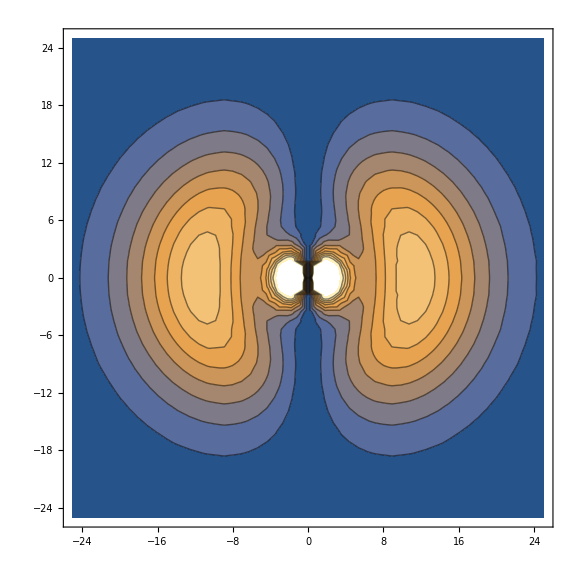

```mathematica
ContourPlot[ (√(1-z^2/(x^2+z^2)))(ⅇ^(-2/5 √(x^2+z^2)) √(x^2+z^2)  (3750-1125 √(x^2+z^2)+90 (x^2+z^2)+2 (x^2+z^2)^(3/2)))/(10986328125π),{x,-25,25},{z,-25,25},ImageSize->Large,Contours->Automatic]
```